This is the original version of the model, with no intraspecific variation (Fox and Vasseur 2008).

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
```

{{Nc→InterpolatingFunction[{{0., 2000.}}, <>],R1→InterpolatingFunction[{{0., 2000.}}, <>],R2→InterpolatingFunction[{{0., 2000.}}, <>],u→InterpolatingFunction[{{0., 2000.}}, <>]}}

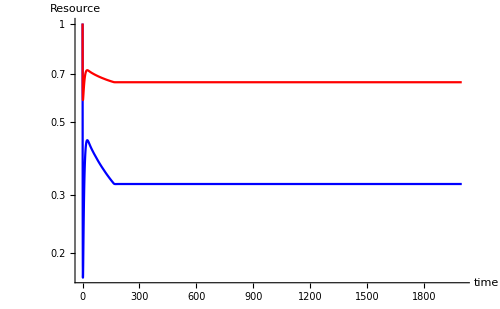

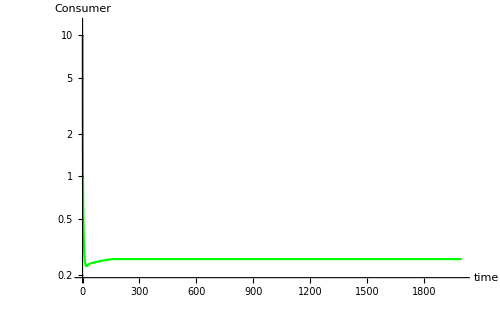

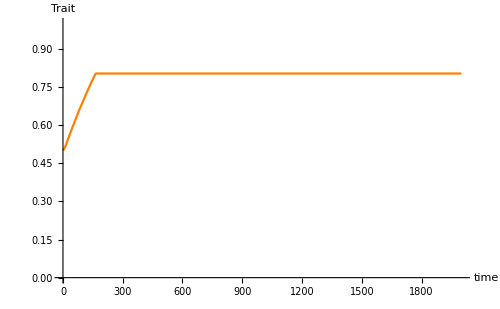

```mathematica
h=10000; (*Controls the steepness of trade-off function; this particular one is very steep*)
w=0.1; (*wash out rate of resources*)
e={0.5,1}; (*units of consumer produced for every unit of resource*)
v=0.01; (*rate of evolution/trait change*)
s={1,1}; (*inflow concentration of resources*)

g[u_,R1_,R2_]:=
Min[e[[1]]*u*R1,e[[2]]*(1-u)*R2]; (*controls the growth of consumer*)
z[R2_,u_,R1_]:=
e[[2]]*R2*(1-u)-e[[1]]*R1*u; (*defines trade-off*)
phi[h_,z_]:=
0.5+Pi^-1*ArcTan[h*z]; (*S-shaped trade-off function*)
d[Nc_]:=
Nc*0.5; (*death rate of consumer*)

tmax=2000;

sol=NDSolve[{Nc'[t]==Nc[t]*(g[u[t],R1[t],R2[t]]-d[Nc[t]]),R1'[t]==w*(s[[1]]-R1[t])-((Nc[t]*g[u[t],R1[t],R2[t]])/e[[1]]),R2'[t]==w*(s[[2]]-R2[t])-((Nc[t]*g[u[t],R1[t],R2[t]])/e[[2]]),u'[t]==v*(phi[h,z[R2[t],u[t],R1[t]]]*(e[[1]]*R1[t]+e[[2]]*R2[t])-e[[2]]*R2[t]),Nc[0]==10,R1[0]==1,R2[0]==1,u[0]==0.5},{Nc,R1,R2,u},{t,0,tmax}]

p1=LogPlot[Evaluate[R1[t]/.sol],{t,0,tmax},PlotRange->All, AxesLabel->{time,Resource},ImageSize->500,PlotStyle -> Blue];
p2=LogPlot[Evaluate[R2[t]/.sol],{t,0,tmax},PlotRange->All, AxesLabel->{time,Resource},ImageSize->500,PlotStyle -> Red];
Show[p1,p2,PlotRange->All]

LogPlot[Evaluate[Nc[t]/.sol],{t,0,tmax},PlotRange->All,AxesLabel->{time,Consumer},ImageSize->500,PlotStyle -> Green]

Plot[Evaluate[u[t]/.sol],{t,0,tmax},PlotRange->{{0,tmax},{0,1}},AxesLabel->{time,Trait},ImageSize->500,PlotStyle -> Orange]
```

```mathematica
In previous forms of this model (i.e. Fox and Vasseur 2008), it' s assumed that ' u' (resource uptake) is the actual trait. 
Now, I need to set up the model so that uptake is a sigmoid function of some trait ' x'.
```

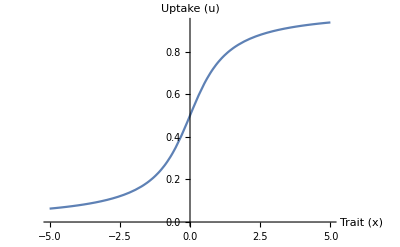

```mathematica
Plot[0.5+Pi^-1*ArcTan[x],{x,-5,5},AxesLabel->{"Trait (x)","Uptake (u)"}]
```

```mathematica
The trait, ' x', is uniformly distributed.
```

Piecewise[{{1/18, -9≤x≤9}, {0, True}}]

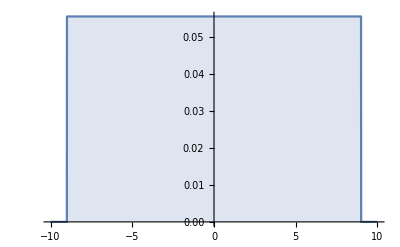

```mathematica
PDF[UniformDistribution[{-9,9}],x]
Plot[%,{x,-10,10},Filling->Axis]
```

```mathematica
Expectation[0.5+Pi^-1*ArcTan[x],x\[Distributed]UniformDistribution[{a,b}]]
```

(0.159155 (3.14159 a-3.14159 b+2. a ArcTan[a]-2. b ArcTan[b]+Log[1/(1.+a^2)]+Log[1.+b^2]))/(a-1. b)

We want to solve for the colimitation uptake (uc) such that uc*e1*R1 = (1 - uc)*e2*R2.

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
```

```mathematica
(*h=10000; (*Controls the steepness of trade-off function; this particular one is very steep*)
w=0.1; (*wash out rate of resources*)
e={0.5,1}; (*units of consumer produced for every unit of resource*)
v=0.01; (*rate of evolution/trait change*)
s={1,1}; (*inflow concentration of resources*)*)

(*This function gives you the expectation for u when x is uniformly distributed with a min a and max b
u[a_,b_]:=
Expectation[0.5+Pi^-1*ArcTan[x],x\[Distributed]UniformDistribution[{a,b}]];*)

x\[Distributed]UniformDistribution[{a,b}];

uc=u/.Solve[{u*e1*R1==(1-u)e2*R2},u]

(*u[x_]:=0.5+Pi^-1*ArcTan[x];
(*Solves for colimitation uptake*)
uc[R1_,R2_]:=
Solve[{u*e[[1]]*R1==(1-u)e[[2]]*R2},u];*)
```

{(e2 R2)/(e1 R1+e2 R2)}

```mathematica
We can then backsolve to figure out what the trait value at this colimitation point will be, xc.
```

```mathematica
xc=x/.Solve[uc==0.5+Pi^-1*ArcTan[x],x]
(*xc[uc_]:=
Solve[uc==0.5+Pi^-1*ArcTan[x],x]*)
```

{Tan[(-1.5708 e1 R1+1.5708 e2 R2)/(1. e1 R1+1. e2 R2)]}

```mathematica
Use xc as the cutoff to weight the growth of a population individuals with trait values that are uniformly distibuted. Individuals with a trait value that falls above uc 
will be limited by resource 1 and those that fall below uc will be limited by resource 2.
```

```mathematica
(*caluclates proportion of population that fall below the colimitation uptake trait value*)
ω[a_,xc_,b_]:=
Abs[xc-a]/Abs[b-a];
(*weighted population growth by proportion of population above and below the colimitation uptake trait value*)
g[ω_,u_,R1_,R2_]:=
(ω*(u*e[[1]]*R1))+((1-ω)*((1-u)*e[[2]]*R2));

(*Solves for the trait variation*)
Solve[Expectation[0.5+Pi^-1*ArcTan[x],x\[Distributed]UniformDistribution[{a,b}]]+σ==a,σ]
```

{{σ→1. a-(0.159155 (3.14159 a-3.14159 b+2. a ArcTan[a]-2. b ArcTan[b]+Log[1/(1.+a^2)]+Log[1.+b^2]))/(a-1. b)}}

```mathematica
Solve[ω==(Tan[(-0.5*Pi*e1*R1+0.5*Pi*e2*R2)/(e1*R1+e2*R2)]-a)/b-a,a]
Solve[ω==(Tan[(-0.5*Pi*e1*R1+0.5*Pi*e2*R2)/(e1*R1+e2*R2)]-a)/b-a,b]
```

{{a→(-ω+(1. Tan[(-1.5708 e1 R1+1.5708 e2 R2)/(e1 R1+e2 R2)])/b)/(1.+1/b)}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b→(-1. a+Tan[(-1.5708 e1 R1+1.5708 e2 R2)/(e1 R1+e2 R2)])/(a+ω)}}

Using these functions for uc, xc, omega and g, I can now write a system of equations that describes population dynamics for the consumer and the resources as well as trait change.

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
```

```mathematica
w=0.1; (*wash out rate of resources*)
e={0.5,1}; (*units of consumer produced for every unit of resource*)
v=0.01; (*rate of evolution/trait change*)
s={1,1}; (*inflow concentration of resources*)

pdf[a_,b_]:=
PDF[UniformDistribution[{a,b}],x];
u[a_,b_]:=
(0.15915494309189535 (Pi* a-Pi* b+2* a *ArcTan[a]-2* b *ArcTan[b]+Log[1/(1+a^2)]+Log[1+b^2]))/(a- b); (*defines uptake as a function of the trait*)
xc[R1_,R2_]:=
{Tan[(-0.5*Pi* e[[1]]* R1+0.5*Pi *e[[2]]* R2)/(e[[1]]* R1+e[[2]]* R2)]}; (*backsolves colimitation trait value*)
ω[a_,xc_,b_]:=
xc-a/b-a;(*caluclates proportion of population that fall below colimitation*)
g[ω_,u_,pdf_,R1_,R2_,a_,b_]:=
(ω*e[[1]]*Integrate[u*pdf,{x,a,xc}]*R1)+((1-ω)*e[[2]]*Integrate[(1-u)*pdf,{x,xc,b}]*R2) ; (*controls weighted growth of consumer*)
d[Nc_]:=
Nc*0.5; (*death rate of consumer*)

(*σ[u_,a_,b_]:=
σ/.Solve[Expectation[u,x\[Distributed]UniformDistribution[{a,b}]]+σ==a,σ]; (*calulates variation around the expectation of the trait distribution*)*)

tmax=2000;

sol=NDSolve[{Nc'[t]==Nc[t]*(g[ω[a[t],xc[R1[t],R2[t]],b[t]],u[a[t],b[t]],pdf[a[t],b[t]],R1[t],R2[t],a[t],b[t]]-d[Nc[t]]),
R1'[t]==w*(s[[1]]-R1[t])-((Nc[t]*g[ω[a[t],xc[R1[t],R2[t]],b[t]],u[a[t],b[t]],pdf[a[t],b[t]],R1[t],R2[t],a[t],b[t]])/e[[1]]),
R2'[t]==w*(s[[2]]-R2[t])-((Nc[t]*g[ω[a[t],xc[R1[t],R2[t]],b[t]],u[a[t],b[t]],pdf[a[t],b[t]],R1[t],R2[t],a[t],b[t]])/e[[2]]),
a'[t]==v*((-ω[a[t],xc[R1[t],R2[t]],b[t]]+(xc[R1[t],R2[t]]/b[t]))/(1+(1/b[t]))),
b'[t]==v*((-a[t]+xc[R1[t],R2[t]])/(a[t]+ω[a[t],xc[R1[t],R2[t]],b[t]])),
Nc[0]==10,R1[0]==1,R2[0]==1,a[0]==0.001,b[0]==0.999},{Nc,R1,R2,a,b},{t,0,tmax}]
```

Integrate::pwrl: Unable to prove that integration limits {xc, a[t]} are real. Adding assumptions may help.

Integrate::pwrl: Unable to prove that integration limits {xc, b[t]} are real. Adding assumptions may help.

Integrate::pwrl: Unable to prove that integration limits {xc, a[t]} are real. Adding assumptions may help.

General::stop: Further output of Integrate :: pwrl will be suppressed during this calculation.

NDSolve::ndinid: Initial condition Sign[Max[0.001  - 1.\ x, -0.999 + x]] is not in the range specified by the discrete variable NDSolve`s$133101.

NDSolve::ndinid: Initial condition Sign[Max[0.001  - 1.\ x, -0.999 + x]] is not in the range specified by the discrete variable NDSolve`s$133802.

NDSolve[{Nc'[t]=={Nc[t] (-0.5 Nc[t]+(∫_xc^b[t] (1-(0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]))/(a[t]-b[t])) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}])ⅆx) R2[t] (1+a[t]+a[t]/b[t]-Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])])+0.5 (∫_a[t]^xc (0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}]))/(a[t]-b[t])ⅆx) R1[t] (-a[t]-a[t]/b[t]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]))},R1'[t]=={0.1 (1-R1[t])-2. Nc[t] ((∫_xc^b[t] (1-(0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]))/(a[t]-b[t])) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}])ⅆx) R2[t] (1+a[t]+a[t]/b[t]-Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])])+0.5 (∫_a[t]^xc (0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}]))/(a[t]-b[t])ⅆx) R1[t] (-a[t]-a[t]/b[t]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]))},R2'[t]=={0.1 (1-R2[t])-Nc[t] ((∫_xc^b[t] (1-(0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]))/(a[t]-b[t])) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}])ⅆx) R2[t] (1+a[t]+a[t]/b[t]-Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])])+0.5 (∫_a[t]^xc (0.159155 (π a[t]+2 a[t] ArcTan[a[t]]-π b[t]-2 ArcTan[b[t]] b[t]+Log[1/(1+a[t]^2)]+Log[1+b[t]^2]) (Piecewise[{{1/(-a[t]+b[t]), a[t]≤x≤b[t]}, {0, True}}]))/(a[t]-b[t])ⅆx) R1[t] (-a[t]-a[t]/b[t]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]))},a'[t]=={(0.01 (a[t]+a[t]/b[t]-Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]/b[t]))/(1+1/b[t])},b'[t]=={(0.01 (-a[t]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])]))/(-a[t]/b[t]+Tan[(-0.785398 R1[t]+1.5708 R2[t])/(0.5 R1[t]+R2[t])])},Nc[0]==10,R1[0]==1,R2[0]==1,a[0]==0.001,b[0]==0.999},{Nc,R1,R2,a,b},{t,0,2000}]

```mathematica
PDF[UniformDistribution[{a,b}]]
PDF[UniformDistribution[{a,b}],x]
```

Function[x,Piecewise[{{1.02041, 0.01≤x≤0.99}, {0, True}}],Listable]

Piecewise[{{1.02041, 0.01≤x≤0.99}, {0, True}}]

Collapse a and b to one parameter. 
Be aware that not defining a<b could cause numerical issues.

```mathematica
h=10000;
w=0.1;(*wash out rate of resources*)
e={{0.5,1},{1,0.5}};(*units of consumer produced for every unit of resource*)
v=0.01;(*rate of evolution/trait change*)
s={1,1};(*inflow concentration of resources*)
d=0.01;(*death rate of consumer*)
u1[a_,b_,xc_]:=Which[a-1. b<0.&&b-1. xc<0.,1/(a-1. b) 0.15915494309189535 (3.141592653589793 a-3.141592653589793 b+2. a ArcTan[a]-2. b ArcTan[b]-1. Log[1. +a^2]+Log[1. +b^2]),a-1. b<0.&&a-1. xc<0.&&b-1. xc≥0.,1/(a-1. b) 0.15915494309189535 (3.141592653589793 a-3.141592653589793 xc+2. a ArcTan[a]-2. xc ArcTan[xc]-1. Log[1. +a^2]+Log[1. +xc^2]),True,0.]
u2[a_,b_,xc_]:=Which[a-1. xc≥0.&&a-1. b<0.,1/(a-1. b) 0.15915494309189535 (3.141592653589793 a-3.141592653589793 b+2. a ArcTan[a]-2. b ArcTan[b]-1. Log[1. +a^2]+Log[1. +b^2]),a-1. b<0.&&a-1. xc<0.&&b-1. xc>0.,1/(a-1. b) 0.15915494309189535 (-3.141592653589793 b+3.141592653589793 xc-2. b ArcTan[b]+2. xc ArcTan[xc]+Log[1. +b^2]-1. Log[1. +xc^2]),True,0.]
xc[r1_,r2_,y1_,y2_]:=Tan[(-0.5*Pi*y1*r1+0.5*Pi*y2*r2)/(y1*r1+y2*r2)];(*backsolves colimitation trait value*)
ω[a_,xc_,b_]:=Which[xc<a,0,a<xc<b,(xc-a)/(b-a),xc>b,1];(*caluclates proportion of population that fall below colimitation*)
g[ω_,u1_,u2_,r1_,r2_,y1_,y2_]:=(ω*y1*u1*r1)+((1-ω)*y2*u2*r2);(*controls weighted growth of consumer*)
tmax=10000;

loop[a1_,b1_,a2_,b2_,x_]:=If[a1≤b1&&a2≤b2,Module[{tmax=x},sol=NDSolve[{Nc1'[t]==Nc1[t]*(g[ω[a1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]],b1],u1[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],u2[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]-d),Nc2'[t]==Nc2[t]*(g[ω[a2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]],b2],u1[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],u2[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]-d),R1'[t]==w*(s[[1]]-R1[t])-((Nc1[t]*g[ω[a1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]],b1],u1[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],u2[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]])/e[[1]][[1]])-((Nc2[t]*g[ω[a2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]],b2],u1[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],u2[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]])/e[[2]][[1]]),R2'[t]==w*(s[[2]]-R2[t])-((Nc1[t]*g[ω[a1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]],b1],u1[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],u2[a1,b1,xc[R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]]],R1[t],R2[t],e[[1]][[1]],e[[1]][[2]]])/e[[1]][[2]])-((Nc2[t]*g[ω[a2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]],b2],u1[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],u2[a2,b2,xc[R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]]],R1[t],R2[t],e[[2]][[1]],e[[2]][[2]]])/e[[2]][[2]]),WhenEvent[Abs[Nc1[t]]<1.0*10^-6,Nc1[t]->0.],WhenEvent[Abs[Nc2[t]]<1.0*10^-6,Nc2[t]->0.],Nc1[0]==5,Nc2[0]==5,R1[0]==1,R2[0]==1},{Nc1,Nc2,R1,R2},{t,0,tmax},Method->{"DiscontinuityProcessing"->False}];
Evaluate[{Nc1[tmax],Nc2[tmax]}/.sol]],"NA"]
```

```mathematica
x=10000;
loopsol2=Table[{a1,b1,a2,b2,(a1+b1)/2,(a2+b2)/2,loop[a1,b1,a2,b2,x]},{a1,-5.0,5.0,0.5},{b1,-5.0,5.0,0.5},{a2,-5.0,5.0,0.5},{b2,-5.0,5.0,0.5}];
```

```mathematica
(*Exports Data from Table as 3 columns*)
loopsol2//MatrixForm;
loopsol3=Flatten[loopsol2];

solLength=Length[loopsol3];
ColumnNumber=3;

loopsol4=Table[{loopsol3[[i]],loopsol3[[i+1]],loopsol3[[i+2]]},{i,1,solLength-ColumnNumber-1,ColumnNumber}];
loopsol4//MatrixForm;

Export["variationloop_x2.csv",loopsol4];
```

```mathematica
pars[a_,b_]:=If[a≤b,(b-a),"NA"];
params=Transpose@Table[{a,b,pars[a,b]},{a,-5.0,5.0,0.1},{b,-5.0,5.0,0.1}];
```

```mathematica
(*Exports Data from Table as 3 columns*)
params//MatrixForm;
Dimensions[params];

params2=Flatten[params];
parsLength=Length[params2];
ColumnNumber=3;

params3=Table[{params2[[i]],params2[[i+1]],params2[[i+2]]},{i,1,parsLength-ColumnNumber-1,ColumnNumber}];
params3//MatrixForm;

Export["test4.csv",params3];
```

```mathematica
xc[r1_,r2_,y1_,y2_]:=Tan[(-0.5*Pi*y1*r1+0.5*Pi*y2*r2)/(y1*r1+y2*r2)];
```

```mathematica
xc[20,10,0.5,1]
```

0.

```mathematica
xc[20,10,1,0.5]
```

-1.37638

```mathematica
u[x_]:=0.5+Pi^-1*ArcTan[x];
```

```mathematica
(d/(y1*(b-a)))*Integrate[1/(0.5+Pi^-1*ArcTan[x]),{x,a,b}]
```

```mathematica
Integrate[1/(0.5+Pi^-1*TrigToExp[ArcTan[x]]),{x,a,b}]
```

```mathematica
Integrate[1/x,{x,a,b}]
```

ConditionalExpression[-Log[a]+Log[b],((Re[b]<0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[b]<Im[a]<0||(a∈Reals&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>(Im[a] Re[b])/Im[b])))||(b∈Reals&&(Im[a]<0||(a∈Reals&&(Re[a]<Re[b]||Re[b]<Re[a]<Re[b]/2+1/2 √(Re[b]^2)))||Im[a]>0))||(Im[b]>0&&((Im[a]<0&&Re[a]>(Im[a] Re[b])/Im[b])||(a∈Reals&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[a]>Im[b]))))||(Re[b]==0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<0||Re[a]>0))||Im[b]<Im[a]<0||(a∈Reals&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>0)))||(Im[b]>0&&((Im[a]<0&&Re[a]>0)||(a∈Reals&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<0||Re[a]>0))||Im[a]>Im[b]))))||(Re[b]>0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[b]<Im[a]<0||(a∈Reals&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>(Im[a] Re[b])/Im[b])))||(b∈Reals&&(Im[a]<0||(a∈Reals&&(Re[b]/2-1/2 √(Re[b]^2)<Re[a]<Re[b]||Re[a]>Re[b]))||Im[a]>0))||(Im[b]>0&&((Im[a]<0&&Re[a]>(Im[a] Re[b])/Im[b])||(a∈Reals&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[a]>Im[b])))))&&((a/(a-b)≠0&&Re[a/(-a+b)]≥0)||Im[a/(-a+b)]≠0||Re[a/(a-b)]>1)&&((Im[a]≥0&&Re[a/(a-b)]≥1&&Im[a]≤Im[b])||(Im[a]≥0&&Re[a/(-a+b)]≥0&&Im[a]≤Im[b])||(Im[a]≥0&&Im[a]≤Im[b]&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Im[b]≥0&&Re[a/(a-b)]≥1)||(Im[a]≥Im[b]&&Im[b]≥0&&Re[a/(-a+b)]≥0)||(Im[a]≥Im[b]&&Im[b]≥0&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Re[a/(a-b)]≥1&&Im[a]≤0)||(Im[a]≥Im[b]&&Re[a/(a-b)]≥1&&Im[b] Re[a]≤Im[a] Re[b])||(Im[a]≥Im[b]&&Re[a/(-a+b)]≥0&&Im[a]≤0)||(Im[a]≥Im[b]&&Re[a/(-a+b)]≥0&&Im[b] Re[a]≤Im[a] Re[b])||(Im[a]≥Im[b]&&Im[a]≤0&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Im[b] Re[a]≤Im[a] Re[b]&&Im[a/(-a+b)]≠0)||(Im[b] Re[a]≥Im[a] Re[b]&&Re[a/(a-b)]≥1&&Im[a]≤Im[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Re[a/(-a+b)]≥0&&Im[a]≤Im[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Im[a]≤Im[b]&&Im[a/(-a+b)]≠0)||(Re[a/(a-b)]≥1&&Im[a]≤Im[b]&&Im[b]≤0)||(Re[a/(-a+b)]≥0&&Im[a]≤Im[b]&&Im[b]≤0)||(Im[a]≤Im[b]&&Im[b]≤0&&Im[a/(-a+b)]≠0))]